```mathematica
<<AlexTools`ALXTools`

harmonics=<|
"Minor Second"-><|"val"-> 16/15,"placement"->Automatic|>,
"Major Second"-><|"val"->9/8,"placement"->Automatic|>,
"Minor Third"-><|"val"->6/5,"placement"->Before|>,
"Major Third"-><|"val"->5/4,"placement"->Automatic|>,
"Perfect Fourth"-><|"val"->4/3,"placement"->Automatic|>,
"Tritone"-><|"val"->7/5.,"placement"->Automatic|>,
"Perfect Fifth"-><|"val"->3/2,"placement"->Automatic|>,
"Minor Sixth"-><|"val"->8/5,"placement"->Automatic|>,
"Major Sixth"-><|"val"->5/3,"placement"->Before|>,
"Augmented Sixth"-><|"val"->7/4,"placement"->Before|>,
"Minor Seventh"-><|"val"->9/5,"placement"->Before|>,
"Major Seventh"-><|"val"->15/8,"placement"->Before|>
|>;
{MTnames,f2f1ratios,f1f2ratios,f1values}={Keys[harmonics],
1. Normal[Dataset[harmonics][Values,"val"]],1./ Normal[Dataset[harmonics][Values,"val"]],540/f2f1ratios};
TableForm[ {MTnames,f2f1ratios,f1f2ratios,f1values}ᵀ,TableHeadings->{None, {"Harmonics","f2/f1 ratios","f1/f2 ratios","f1 values"}}]

ratiosOfInterest={0.2,0.5,0.6,2/3,0.75,1,1.333,3/2,1.666,2,5};
```

Harmonics | f2/f1 ratios | f1/f2 ratios | f1 values
Minor Second | 1.06667 | 0.9375 | 506.25
Major Second | 1.125 | 0.888889 | 480.
Minor Third | 1.2 | 0.833333 | 450.
Major Third | 1.25 | 0.8 | 432.
Perfect Fourth | 1.33333 | 0.75 | 405.
Tritone | 1.4 | 0.714286 | 385.714
Perfect Fifth | 1.5 | 0.666667 | 360.
Minor Sixth | 1.6 | 0.625 | 337.5
Major Sixth | 1.66667 | 0.6 | 324.
Augmented Sixth | 1.75 | 0.571429 | 308.571
Minor Seventh | 1.8 | 0.555556 | 300.
Major Seventh | 1.875 | 0.533333 | 288.

### Introduction & prelim data 23.07.2025

This notebook was created to generate 2-tone pairs for hair cells to be applied to Thomas Effertz’s lab in Goettingen.

Here, the experimental setup is made to stimulate hair cells with one of two ways: 
- probe actuator (a metal rod) only for outer hair cells
- fluid jet (more modern, and can address both inner and outer hair cells.

The cells are patch-clamped and we measure the MET current. This is what we can do here in this lab.

The typical stimuli have a duration ~100ms to avoid damage and cell fatigue.

```mathematica
Clear[cubic]
cubic[targetDP_:60,targetRatio_:1.5]:=Block[{f1,f2},

Quiet@Solve[{2f1-f2==targetDP,f2/f1==targetRatio}]

]

(* This is made to help us identify frequencies of interest that target the CUBIC distortion*)
TableForm[Flatten[Table[1. {f1,f2,ratio}/.cubic[60,ratio],{ratio,ratiosOfInterest}],1],TableHeadings->{None, (Style[#,Black,16]&/@{"f1","f2","ratio"})}]
```

f1 | f2 | ratio
33.3333 | 6.66667 | 0.2
40. | 20. | 0.5
42.8571 | 25.7143 | 0.6
45. | 30. | 0.666667
48. | 36. | 0.75
60. | 60. | 1.
89.955 | 119.91 | 1.333
120. | 180. | 1.5
179.641 | 299.281 | 1.666
1. f1 |  | 
1. f2 |  | 
2. |  | 
-20. | -100. | 5.

```mathematica
Table[{f1,2f1-60},{f1,100,1000}];
```

```mathematica
{619,1178}
```

{619,1178}

```mathematica
2 620-1180
```

60

```mathematica
sr = 50000;
test=Import["C:\\Users\\hadif\\Proton Drive\\c.a.alampounti\\My files\\Uni\\UCL\\Projects\\04_two-tone_hair_cells\\multisine\\100 - 160 Hz 525ms -repositioned pusher.asc"][[;;-2]];
```

```mathematica
test[[4]] (* voltage is the membrane potential, current is the MET, Adc is the stimulus voltage.*)
```

{Time[s],Current[A],Time[s],Adc-0[V],Time[s],Voltage[V]}

NOTE: The stimulus starts after 20ms. Prior to this there is a testing stage is a diagnostic test to ensure that the cell capacitance has been compensated.

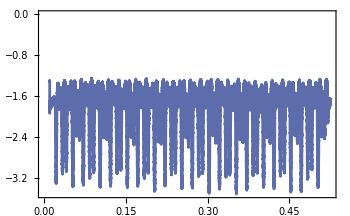

```mathematica
gap = Round[sr 20 10^-3];
ListLinePlot[MapAt[# 10^10&,test[[5+gap;;,{1,2}]],{All,2}]]
```

```mathematica
1120-620
1120+620
2 620-1120
```

500

1740

120

### Showing that the nerve automatically gets f1-f2 and f1+f2 by virtue of having a rectified signal.

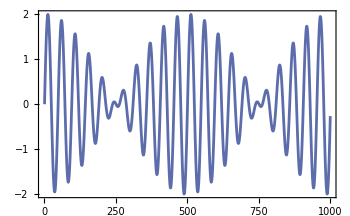
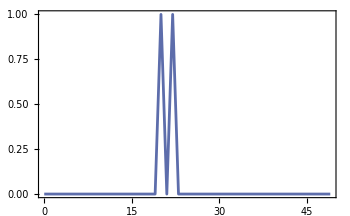

```mathematica
t=Table[Sin[2π 20 t]+Sin[2π 22 t],{t,0,1-1/1000,1/1000}];
{ListLinePlot[t], ListLinePlot[fourier[t,1000,50]]}
```

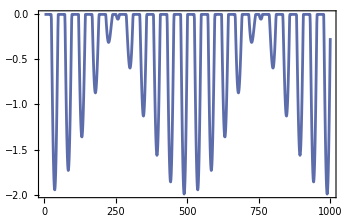
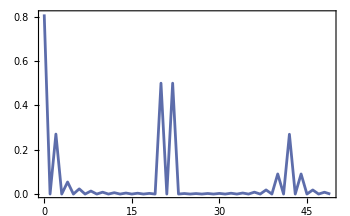

```mathematica
t2=1. t/.x_/;x>0->0;
{ListLinePlot[t2], ListLinePlot[fourier[t2,1000,50]]}
```

```mathematica
2  600-480.
```

720.

```mathematica
120
360
960
```

120

360

960

```mathematica
f1 = 6.6666
f2=33.33333

2f2-f1
f2-f1
f1-f2
```

6.6666

33.3333

60.0001

26.6667

-26.6667

```mathematica
2
```

2

```mathematica
13.68
19.8
26.6
39.3
47
67
```

13.68

19.8

26.6

39.3

47

67

### Testing whether beats vs 2-tone is a viable alternative

Demonstration that sin[a]+ sin[b]== sin[(a+b)/2]sin[(a-b)/2]

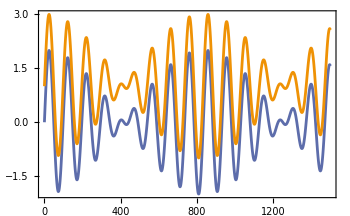
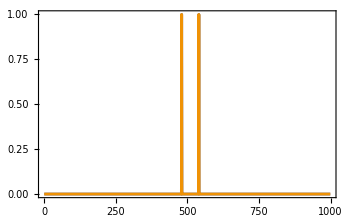

```mathematica
sRate=50000;
t=Table[Sin[2π 480 t]+Sin[2π 540 t],{t,0,1-1/sRate,1/sRate}];
t2=Table[2Sin[2π 30 t+π/2]Sin[2π 510 t],{t,0,1-1/sRate,1/sRate}];

{ListLinePlot[{t[[;;1500]],t2[[;;1500]]+1}], ListLinePlot[{fourier[t,sRate,1000],fourier[t2,sRate,1000]}]}
```

Showing that 
(1+Sin[2π 60 t+π/2])Sin[2π 510 t] 
is equal to 
1.0 Sin[2π 510 t] + 0.5 Sin[2π 450 t] + 0.5 Sin[2π 570 t]

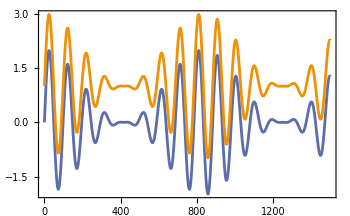
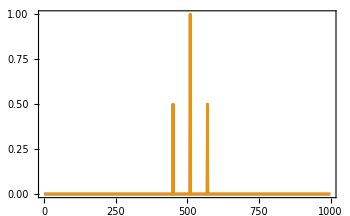

```mathematica
t3=Table[(1+Sin[2π 60 t+π/2])Sin[2π 510 t],{t,0,1-1/sRate,1/sRate}];
t4=Table[Sin[2π 510 t]+0.5Sin[2π 450 t]+0.5Sin[2π 570 t],{t,0,1-1/sRate,1/sRate}];
{ListLinePlot[{t3[[;;1500]],t4[[;;1500]]+1}], ListLinePlot[{fourier[t3,sRate,1000],fourier[t4,sRate,1000]}]}
```

Why do we care about this?
This is Rico’s 3 Tone experiment.
This was created as a means to keep the “carrier” frequency as 510 Hz but “tighten” the inter-pulse interval slightly.
He found that by doing that, the nerve responses are qualitatively stronger at the expense of a delayed onset of first nerve response and the eventual nerve fatigue onset occurring at the same time as a 2T stimulus. You can see the discussion in OneNote labelled “Discussion with Rico”.

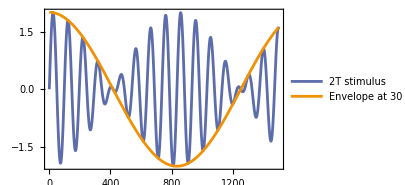
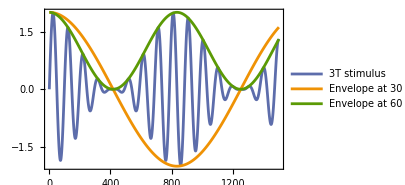

```mathematica
numOfPoints=1500;
{ListLinePlot[{Table[(2Sin[2π 30 t+π/2])Sin[2π 510 t],{t,0,numOfPoints/sRate-1/sRate,1/sRate}],
Table[2Cos[2π 30 t](*(1+Sin[2π 60 t+π/2])*)(*2(Sin[2π 30 t+π/2])^2*),{t,0,numOfPoints/sRate-1/sRate,1/sRate}]},PlotRange->{-2,2},PlotLegends->Placed[{"2T stimulus","Envelope at 30 Hz"},Above],ImageSize->300],
ListLinePlot[{Table[(1+Sin[2π 60 t+π/2])Sin[2π 510 t],{t,0,numOfPoints/sRate-1/sRate,1/sRate}],
Table[2Cos[2π 30 t](*(1+Sin[2π 60 t+π/2])*),{t,0,numOfPoints/sRate-1/sRate,1/sRate}],
Table[1+ Cos[2π 60 t](*(1+Sin[2π 60 t+π/2])*),{t,0,numOfPoints/sRate-1/sRate,1/sRate}]

},PlotRange->{-2,2},PlotLegends->Placed[{"3T stimulus","Envelope at 30 Hz","Envelope at 60 Hz"},Above],ImageSize->300]}
```

The rationale as to why this particular combination of 3 tones is useful/important still evades me:

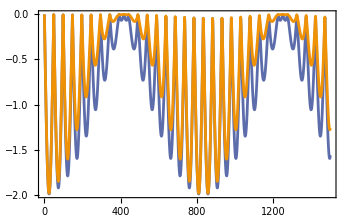

```mathematica
ListLinePlot[-Abs[#[[;;1500]]]&/@{t2,t4}]
```

```mathematica
Sin[2π 510 t]+0.5(Sin[2π 450 t]+Sin[2π 570 t])
Sin[2π 510 t]+Sin[2π 120 t]Sin[2π 510 t]
Sin[2π 510 t](1+Sin[2π 120 t])
```

### 2-tone series on hair cells

```mathematica
sRate = 100000;
dir="C:\\Users\\hadif\\Proton Drive\\c.a.alampounti\\My files\\Uni\\UCL\\Projects\\04_two-tone_hair_cells\\Data 2025-07-24\\freq scanning series\\"; (* directory where data is saved *)
fnames=FileNames["*.asc",dir,∞]; (* find all ASCII data *)
fnamesSorted=SortBy[fnames,ToExpression[StringCases[#,DigitCharacter..][[-1]]]&]; (* Sort the data based on labelled frequency *)
bufferValues=Round[0.05 sRate]; (* when experiment begins in seconds *)
freqsUsed=Sort[ToExpression[StringCases[#,DigitCharacter..][[-1]]]&/@fnames]; (* identify the frequencies used based on file label *)

data=Import[#][[bufferValues+4;;-bufferValues-2,{1,2}]]&/@fnamesSorted; (*{"Time[s]","Current[A]","Time[s]","Adc-0[V]","Time[s]","Voltage[V]"}*)
(* NOTE: The data above are MULTIPLEXED, which means that the TIME columns are NOT the same.*)
(* NOTE 2: Each buffer has an offset to account for text fluff. The data saved does not contain anything from the other columns *)
```

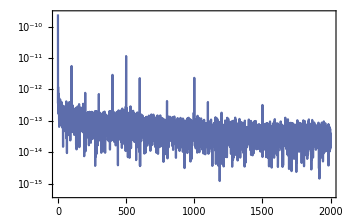
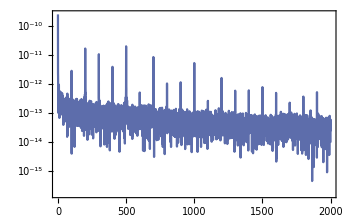

```mathematica
ListLogPlot[fourier[#[[;;,2]],sRate,2000],Joined->True]&/@data[[;;2]]
```

```mathematica
data2=Table[Prepend[#,freqsUsed[[i]]]&/@fourier[10^9 data[[i]][[;;,2]],sRate,2000],{i,Length@freqsUsed}];
```

```mathematica
ListDensityPlot[Flatten[data2,1],PlotRange->Full]
```

$Aborted

```mathematica
ListLinePlot3D[data2,PlotRange->Full,ScalingFunctions->"Log",AxesLabel->{"Stim Frequency [Hz]","Response Frequency [Hz]","Amp [nA]"}]
```

-Graphics3D-